```mathematica
(* load hughes.nb *)
```

```mathematica
M=1.4*msun
R=10*km
myr=rg*myrperrg
rg=G*M/c^2
tg=rg/c
Print["Rrat"];
R/rg
(*
myomegak=omegak/tg//.{a->0}
f=2*Pi*myomegak//.{r->R,a->0}
*)
my2vk=omegak*r
my2vk//.{r->R/rg,a->0}
f=(1/tg)*1/(2*Pi)*omegak//.{r->R/rg,a->0}
```

2.7846×10^33

1000000

333648.

206718.

6.89536×10^-6

Rrat

4.83752

r/(a+r^(3/2))

0.454662

2169.35

```mathematica
(*
http://www.sciencedirect.com/science?_ob=ArticleURL&_udi=B6VNJ-4S32NTH-3&_user=145269&_rdoc=1&_fmt=&_orig=search&_sort=d&_docanchor=&view=c&_searchStrId=948198852&_rerunOrigin=google&_acct=C000012078&_version=1&_urlVersion=0&_userid=145269&md5=157665af263cac538227cb193f23061a
*)
```

```mathematica
maxf=3*760
1./maxf*1000
```

2280

0.438596

```mathematica
1/f*1000
```

0.460968

```mathematica
oldomegak=Sqrt[G*M/r^3]//.{r->10*km}
oldf=oldomegak/(2*Pi)
oldvk=r*oldomegak//.{r->10*km}
oldvkperc=oldvk/c
```

13630.4

2169.35

1.36304×10^10

0.454662

```mathematica
abh=.98
M=14.4*msun
myrperrg=(myrisco//.{a->abh})
myr=rg*myrperrg
rg=G*M/c^2
tg=rg/c
(* mv^2/r = GMm/r^2 -> romega^2 = GM/r^2 -> omega^2 = GM/r^3 *)
(*omegak=Sqrt[G*M]/(R^(3/2)+abh)*)
myomegak=omegak/tg//.{a->abh}
myvk=myomegak*r*rg
myomegah=omegah/tg//.{a->abh}
Print["f"];
f=myomegak/(2*Pi)
fbh=myomegah/(2*Pi)
Print["tau"];
tau=1/f
taubh=1/fbh
```

0.98

2.86416×10^34

1.61403

333648.

2.12624×10^6

0.0000709237

14099.7/(0.98+r^(3/2))

(2.99792×10^10 r)/(0.98+r^(3/2))

5762.18

f

2244.03/(0.98+r^(3/2))

917.079

tau

0.000445627 (0.98+r^(3/2))

0.00109042

```mathematica
(myvk//.{r->R/rg})/c
crap=f//.{r->R/rg}
1/crap*1000
```

0.361075

1722.81

0.580446

```mathematica
(* ADAF *)
(* http://www.iop.org/EJ/article/0004-637X/679/2/984/74028.text.html *)
```

```mathematica
jin=l//.{a->abh}
alpha=0.1
cs=H/r*(r*omegak)
frac=1
HOR=0.9
H=r*HOR
vr = -alpha*r*cs^2/(frac*omegak*r^2-jin)//.{a->abh}
```

1.68267

0.1

(0.9 r)/(a+r^(3/2))

1

0.9

0.9 r

-(0.081 r^3)/((0.98+r^(3/2))^2 (-1.68267+r^2/(0.98+r^(3/2))))

```mathematica
binaryorbitperiod=30*(24*60*60)
distance=0.5*AU
disksize=0.3*AU
routdisk=disksize/rg
```

2592000

7.4799×10^12

4.48794×10^12

2.11074×10^6

```mathematica
(*lowqpo=67*)
lowqpo=168
sol=FindRoot[lowqpo==f,{r,10}]
routlowqpo=r//.sol[[1]]
```

168

{r→5.35079}

5.35079

```mathematica
Eqpo=((13+30)/2)/1000*ergPmev
Solve[Eqpo==(gam-1)*me*c^2,gam]
```

3.44468×10^-8

{{gam→1.04207}}

-(0.081 r^3)/((0.98+r^(3/2))^2 (-1.68267+r^2/(0.98+r^(3/2))))

1.61403

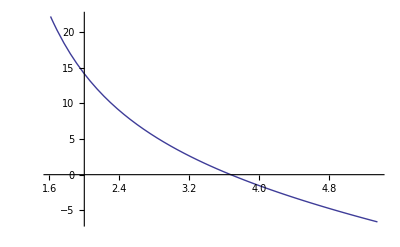

-10.5064

Time in minutes

-0.175107

Time in hours

-0.00291845

Time in days

-0.000121602

Time in years

-3.32928×10^-7

```mathematica
rout=routlowqpo;
(*rout=routdisk*)
myvr=vr//.{a->abh}
therisco=myrisco//.{a->abh}
Plot[1/myvr,{r,rout,therisco}]
totaltime=Integrate[1/myvr,{r,rout,therisco}]
Print["Time in minutes"];
totaltime/(60)
Print["Time in hours"];
totaltime/(60*60)
Print["Time in days"];
totaltime/(60*60*24)
Print["Time in years"];
totaltime/(60*60*24*365.25)
```

```mathematica
45000/5/12
```

750

```mathematica
thetaj=5/180*Pi
gamma=10.
thetaj*gamma
```

π/36

10.

0.872665